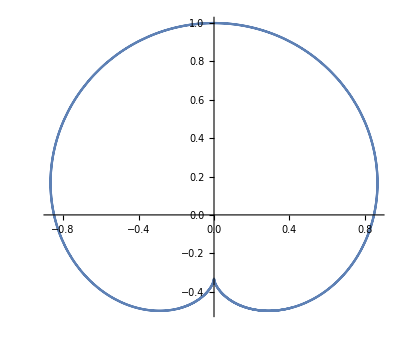

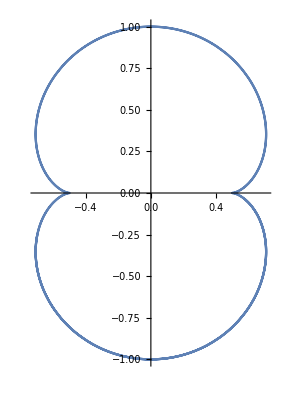

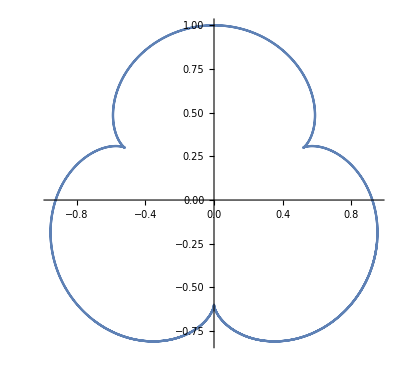

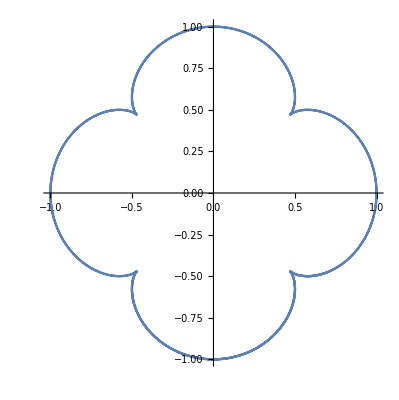

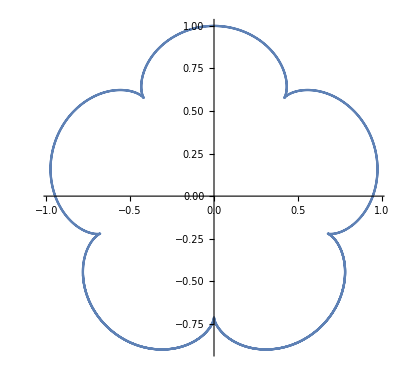

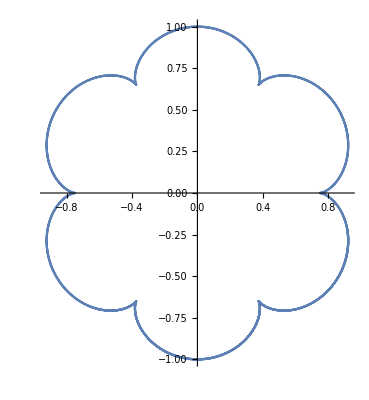

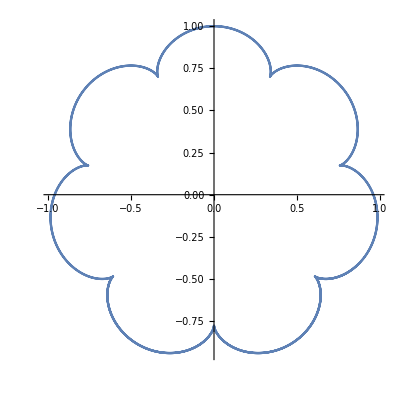

```mathematica
ClearAll["Global`*"];
F[x_,y_,t_,a_,k_]:=(Cos[2^(1-k) π t]-Cos[2^(1-k) a π t]) x+Sin[2^(1-k) (-1+a) π t]+y (Sin[2^(1-k) π t]-Sin[2^(1-k) a π t]);
Fd[x_,y_,t_,a_,k_]:= 2^(1-k) π ((-1+a) Cos[2^(1-k) (-1+a) π t]+(Cos[2^(1-k) π t]-a Cos[2^(1-k) a π t]) y+x (-Sin[2^(1-k) π t]+a Sin[2^(1-k) a π t]));
parametricFunc[t_,a_,k_]:={x,y}/.(Solve[F[x,y,t,a,k]==0&&Fd[x,y,t,a,k]==0,{x,y}]);
plot[a_,k_,from_,to_]:=ParametricPlot[parametricFunc[t,a,k],{t,from,to}];

(*eqn2={F[x,y,t,a,k]==0,Fd[x,y,t,a,k]==0};
Print[FullSimplify[Eliminate[eqn2,t]]]*)
k=1;
plot[2,k,E^k,E^(k+1)]
plot[3,k,E^k,E^(k+1)]
plot[4,k,E^k,E^(k+1)]
plot[5,k,E^k,E^(k+1)]
plot[6,k,E^k,E^(k+1)]
plot[7,k,E^k,E^(k+1)]
plot[8,k,E^k,E^(k+1)]
```